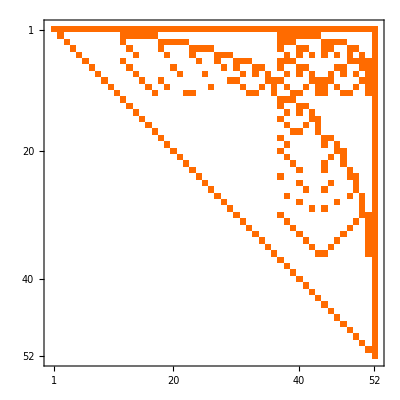

```mathematica
ConversionMatrix["E","C"]//MatrixPlot
```

```mathematica
MatrixToGraph[mat_,nodes_]:=Block[{edges={},from,to,vertices},
Table[
from=nodes[[x]];
Table[
to=nodes[[y]];
If[mat[[x,y]]==1&&x≠y,AppendTo[edges,from->to]]
,{y,Length[nodes]}
]
,{x,Length[nodes]}
];
edges=DeleteDuplicates[edges];
vertices = Table[s-> Rotate[SymbolToLabel[ s],Pi/6],{s,nodes}];
Graph[edges,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->vertices,AspectRatio->1]
]
```

```mathematica
Bases["G"]
```

<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>

```mathematica
SubgraphQ
```

```mathematica
IsomorphicGraphQ[
With[{base="G"},MatrixToGraph[ConversionMatrix[base,"C"],Bases[base,"Variables"]]],
With[{base="G"},MatrixToGraph[ConversionMatrix[base,"C"],Bases[base,"Variables"]]]
]
```

True

```mathematica
With[{base="F"},Sort[EdgeList[MatrixToGraph[ConversionMatrix[base,"C"],Bases[base,"Variables"]]]]]//DeleteDuplicates//Length
```

1152

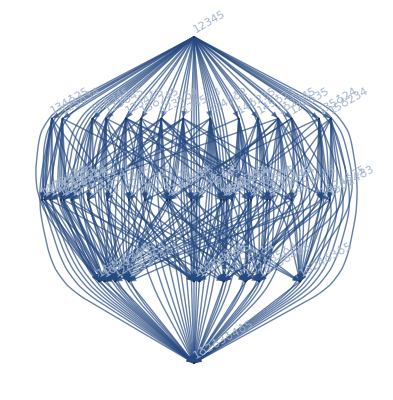

```mathematica
With[{base="G"},MatrixToGraph[ConversionMatrix[base,"C"],Bases[base,"Variables"]]]
```

```mathematica
With[{base="G"},Select[MatrixToGraph[ConversionMatrix[base,"C"],Bases[base,"Variables"]]//GraphDistanceMatrix//Flatten,#≠Infinity&]//Max]
```

1